```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
sn=Import["ame-flower-F.mid","SoundNotes"];
Take[sn[[1]]] (*查看第一小节的10个音符？*)
```

{SoundNote[F4,{0.,0.9},Piano,SoundVolume→0.627451],SoundNote[G4,{0.9,1.2},Piano,SoundVolume→0.627451],SoundNote[E4,{1.2,1.8},Piano,SoundVolume→0.627451],SoundNote[D4,{1.8,2.4},Piano,SoundVolume→0.627451],SoundNote[A4,{2.4,4.8},Piano,SoundVolume→0.627451]}

```mathematica
sn=sn/.{"Piano"->"Harmonica"}
```

{{SoundNote[F4,{0.,0.9},Harmonica,SoundVolume→0.627451],SoundNote[G4,{0.9,1.2},Harmonica,SoundVolume→0.627451],SoundNote[E4,{1.2,1.8},Harmonica,SoundVolume→0.627451],SoundNote[D4,{1.8,2.4},Harmonica,SoundVolume→0.627451],SoundNote[A4,{2.4,4.8},Harmonica,SoundVolume→0.627451]}}

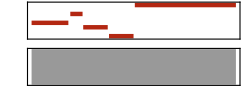

```mathematica
Sound@sn(*//EmitSound*)
```

```mathematica
(*
Xiao 箫
Harmonica 口琴
Violin 小提琴
Bass 大提琴
AudioPitchShift 变调
AudioTimeStretch 变速
Sound[SoundNote["G",1,"Harmonica"]]//EmitSoun
EntityValue["MusicalInstrument","Entities"]
*)
```